```mathematica
ClearAll;
```

-This notebook exports the (force vs relative end-to-end distance) curves of a single filament
-Evaluation of the Free energy for a single filament from a purely mechanical approach
- Inextensible vs extensible filament models: worm-like chain model:
	*countour length L
	*persistence length Lp
	*semi-flexibility L~Lp --> small lateral displacements
	*fully flexible  --> finite lateral disp and finite stretching
Considerations:	
-Filament subject to bending and stretching
-Torsion or twisting neglected
-pinned BCs in the filament ends
- Integration of this filament model requires the initial end-to-end distance of the filament inside a network prior deformation

```mathematica
(*Parametric study*)
```

```mathematica
δ=2;
a=1.2;
T=294;  (*K*)
Lp=16;(*μm*)
r0=1.63;(*μm*)
L = a*r0;
n=15.0/L (*μm^-3*)
kB=1.38*(10^-5);(*pN.μm/K*)
B0=kB*T*Lp;
```

7.66871

```mathematica
(*inextensible holzapfel*)
dw=(π^2*r0*B0)/(L*L)*(((a-1)/(a-λ))^δ-1) ;
```

```mathematica
dw/r0;
```

```mathematica
F={{1,γ,0},{0,1,0},{0,0,1}};
F//MatrixForm
```

(1 | γ | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
m0={{Sin[θ]*Cos[ϕ]},{Sin[θ]*Sin[ϕ]},{Cos[θ]}};
m0//MatrixForm
m=Simplify[F.m0];
aa=m.Transpose[m];
aa//MatrixForm
```

(Cos[ϕ] Sin[θ]
Sin[θ] Sin[ϕ]
Cos[θ])

(Sin[θ]^2 (Cos[ϕ]+γ Sin[ϕ])^2 | Sin[θ]^2 Sin[ϕ] (Cos[ϕ]+γ Sin[ϕ]) | Cos[θ] Sin[θ] (Cos[ϕ]+γ Sin[ϕ])
Sin[θ]^2 Sin[ϕ] (Cos[ϕ]+γ Sin[ϕ]) | Sin[θ]^2 Sin[ϕ]^2 | Cos[θ] Sin[θ] Sin[ϕ]
Cos[θ] Sin[θ] (Cos[ϕ]+γ Sin[ϕ]) | Cos[θ] Sin[θ] Sin[ϕ] | Cos[θ]^2)

```mathematica
m00={Sin[θ]*Cos[ϕ],Sin[θ]*Sin[ϕ],Cos[θ]};
m00//MatrixForm;
mm=Simplify[F.m00];
mm//MatrixForm
λ=Sqrt[mm.mm]
```

(Sin[θ] (Cos[ϕ]+γ Sin[ϕ])
Sin[θ] Sin[ϕ]
Cos[θ])

√(Cos[θ]^2+Sin[θ]^2 Sin[ϕ]^2+Sin[θ]^2 (Cos[ϕ]+γ Sin[ϕ])^2)

```mathematica
λ=Sqrt[1+Sin[θ]^2*(γ*Sin[2*ϕ]+γ*γ*Sin[ϕ]^2)]
```

√(1+Sin[θ]^2 (γ^2 Sin[ϕ]^2+γ Sin[2 ϕ]))

```mathematica
arg=λ^-1*dw*aa*Sin[θ];
arg//MatrixForm;
```

```mathematica
d11c95=Table[{γ,n*NIntegrate[Part[arg,1,1],{ϕ,0,2π},{θ,0,π}]},{γ,0.01,0.3,0.01}]
```

{{0.01,0.00890082},{0.02,0.0356927},{0.03,0.0806459},{0.04,0.144218},{0.05,0.227063},{0.06,0.330052},{0.07,0.454285},{0.08,0.601131},{0.09,0.772252},{0.1,0.969657},{0.11,1.19576},{0.12,1.45343},{0.13,1.74614},{0.14,2.07802},{0.15,2.45405},{0.16,2.88026},{0.17,3.36395},{0.18,3.91409},{0.19,4.54176},{0.2,5.26077},{0.21,6.08855},{0.22,7.0474},{0.23,8.16625},{0.24,9.48334},{0.25,11.0502},{0.26,12.9378},{0.27,15.247},{0.28,18.1255},{0.29,21.7988},{0.3,26.6288}}

```mathematica
d22c95=Table[{γ,n*NIntegrate[Part[arg,2,2],{ϕ,0,2π},{θ,0,π}]},{γ,0.01,0.3,0.01}]
```

{{0.01,0.00714509},{0.02,0.0286444},{0.03,0.0646916},{0.04,0.115614},{0.05,0.181881},{0.06,0.264115},{0.07,0.363105},{0.08,0.479828},{0.09,0.615475},{0.1,0.771479},{0.11,0.949564},{0.12,1.15179},{0.13,1.38061},{0.14,1.63899},{0.15,1.93046},{0.16,2.25932},{0.17,2.63076},{0.18,3.05115},{0.19,3.52834},{0.2,4.07214},{0.21,4.69488},{0.22,5.41233},{0.23,6.24494},{0.24,7.21969},{0.25,8.3729},{0.26,9.7546},{0.27,11.4357},{0.28,13.52},{0.29,16.1656},{0.3,19.6264}}

```mathematica
d33c95=Table[{γ,n*NIntegrate[Part[arg,3,3],{ϕ,0,2π},{θ,0,π}]},{γ,0.01,0.3,0.01}]
```

{{0.01,0.00238099},{0.02,0.00953674},{0.03,0.0215059},{0.04,0.0383534},{0.05,0.0601718},{0.06,0.0870828},{0.07,0.119239},{0.08,0.156827},{0.09,0.200071},{0.1,0.249235},{0.11,0.304632},{0.12,0.366626},{0.13,0.435645},{0.14,0.512185},{0.15,0.596826},{0.16,0.690247},{0.17,0.793243},{0.18,0.906765},{0.19,1.03192},{0.2,1.17003},{0.21,1.32271},{0.22,1.4919},{0.23,1.68},{0.24,1.88996},{0.25,2.12555},{0.26,2.39157},{0.27,2.69435},{0.28,3.04236},{0.29,3.44736},{0.3,3.92624}}

```mathematica
d12c95=Table[{γ,n*NIntegrate[Part[arg,1,2],{ϕ,0,2π},{θ,0,π}]},{γ,0.01,0.3,0.01}]
```

{{0.01,0.175573},{0.02,0.352414},{0.03,0.53181},{0.04,0.715088},{0.05,0.903639},{0.06,1.09894},{0.07,1.30257},{0.08,1.51628},{0.09,1.74197},{0.1,1.98178},{0.11,2.23811},{0.12,2.51372},{0.13,2.81177},{0.14,3.13596},{0.15,3.49062},{0.16,3.88086},{0.17,4.31287},{0.18,4.79412},{0.19,5.33376},{0.2,5.94314},{0.21,6.63653},{0.22,7.43213},{0.23,8.35353},{0.24,9.43186},{0.25,10.7091},{0.26,12.243},{0.27,14.1159},{0.28,16.4483},{0.29,19.4246},{0.3,23.3411}}

```mathematica
19.6264157428797+0.3*23.3411170514071
```

26.6288

```mathematica
(*d23c95=Table[{γ,NIntegrate[n*Part[arg,2,3]*Sin[θ],{ϕ,0,2π},{θ,0,π}]},{γ,0.01,0.3,0.01}]
d13c95=Table[{γ,NIntegrate[n*Part[arg,1,3]*Sin[θ],{ϕ,0,2π},{θ,0,π}]},{γ,0.01,0.3,0.01}]*)
```

```mathematica
(*σ22=NIntegrate[arg22,{ϕ,0,2π},{θ,0,π}]
σ12=NIntegrate[arg12,{ϕ,0,2π},{θ,0,π}]*)
```

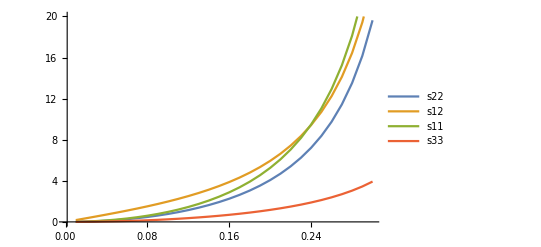

```mathematica
s=ListPlot[{d22c95,d12c95,d11c95,d33c95},Joined->True,PlotRange->{{0.0001,.3},{0.0,20.0}},PlotLegends->{"s22","s12","s11","s33"}]
```

```mathematica
d12=D[Part[arg,1,2], γ];
```

```mathematica
dd12=Table[{γ,NIntegrate[d12,{ϕ,0,2π},{θ,0,π}]},{γ,0.0001,0.3,0.01}];
```

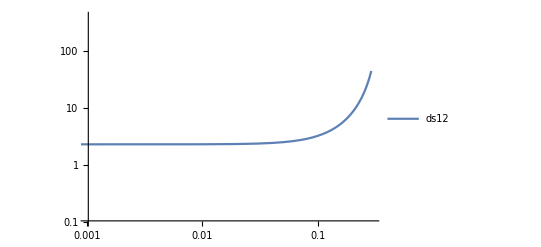

```mathematica
ds=ListLogLogPlot[{dd12},Joined->True,PlotRange->{{0.001,.3},{0.1,400.0}},PlotLegends->{"ds12"}]
```

```mathematica
d22alt=Table[{γ,n*(π^2*B0)/(a*L)*NIntegrate[(1/λ)*(((a-1)/(a-λ))^δ-1)*(Sin[θ]^3*Sin[ϕ]^2-Cos[θ]^2*Sin[θ]),{ϕ,0,2π},{θ,0,π}]},{γ,0.0001,0.3,0.01}]
```

{{0.0001,4.75984×10^-7},{0.0101,0.00485995},{0.0201,0.0192999},{0.0301,0.0434764},{0.0401,0.0776532},{0.0501,0.122208},{0.0601,0.177643},{0.0701,0.244595},{0.0801,0.323858},{0.0901,0.416399},{0.1001,0.52339},{0.1101,0.646244},{0.1201,0.786658},{0.1301,0.946671},{0.1401,1.12874},{0.1501,1.33584},{0.1601,1.57158},{0.1701,1.84038},{0.1801,2.14767},{0.1901,2.5002},{0.2001,2.90647},{0.2101,3.37723},{0.2201,3.92636},{0.2301,4.57195},{0.2401,5.33809},{0.2501,6.25744},{0.2601,7.37539},{0.2701,8.75674},{0.2801,10.4972},{0.2901,12.7439}}

```mathematica
d12alt=Table[{γ,n*(π^2*B0)/(a*L)*NIntegrate[(1/λ)*(((a-1)/(a-λ))^δ-1)*Sin[ϕ]*(Cos[ϕ]+γ*Sin[ϕ])*Sin[θ]^3,{ϕ,0,2π},{θ,0,π}]},{γ,0.01,0.3,0.01}]
```

{{0.01,0.175573},{0.02,0.352414},{0.03,0.53181},{0.04,0.715088},{0.05,0.903639},{0.06,1.09894},{0.07,1.30257},{0.08,1.51628},{0.09,1.74197},{0.1,1.98178},{0.11,2.23811},{0.12,2.51372},{0.13,2.81177},{0.14,3.13596},{0.15,3.49062},{0.16,3.88086},{0.17,4.31287},{0.18,4.79412},{0.19,5.33376},{0.2,5.94314},{0.21,6.63653},{0.22,7.43213},{0.23,8.35353},{0.24,9.43186},{0.25,10.7091},{0.26,12.243},{0.27,14.1159},{0.28,16.4483},{0.29,19.4246},{0.3,23.3411}}

```mathematica
a
```

1.2

```mathematica
λ
```

√(1+Sin[θ]^2 (γ^2 Sin[ϕ]^2+γ Sin[2 ϕ]))

```mathematica
xx=0.0;
yy=1.0;
zz=0;
rw=5.304284881800000*(10^(-2));

t0={{xx},{yy},{0}};
t=Simplify[F.t0];
t//MatrixForm
```

(0.+1. γ
1.
0.)

```mathematica
t00={xx,yy,zz};
t00//MatrixForm;
tt=Simplify[F.t00];
tt//MatrixForm;
λ=Sqrt[tt.tt]
```

√(1.+(0.+1. γ)^2)

```mathematica
θ=ArcCos[Part[tt,3]]
ϕ=ArcTan[Part[tt,1]/Part[tt,2]]
```

1.5708

ArcTan[1. (0.+1. γ)]

```mathematica
dw
```

0.272958 (-1+0.04/((1.2-√(1.+(0.+1. γ)^2))^2))

```mathematica
Part[arg,1,2]*rw
```

(0.0144785 (0.+1. γ) (1/(√(1+1. (0.+1. γ)^2))+(1. γ (0.+1. γ))/(√(1+1. (0.+1. γ)^2))) (-1+0.04/((1.2-√(1+1. ((1. γ^2 (0.+1. γ)^2)/(1+1. (0.+1. γ)^2)+γ Sin[2 ArcTan[1. (0.+1. γ)]])))^2)))/(√(1+1. (0.+1. γ)^2) √(1+1. ((1. γ^2 (0.+1. γ)^2)/(1+1. (0.+1. γ)^2)+γ Sin[2 ArcTan[1. (0.+1. γ)]])))

```mathematica
Part[aa,1,2]
```

(1. (0.+1. γ) (1/(√(1+1. (0.+1. γ)^2))+(1. γ (0.+1. γ))/(√(1+1. (0.+1. γ)^2))))/(√(1+1. (0.+1. γ)^2))

```mathematica
n*(π^2*B0)/(a*L)
```

2.09324